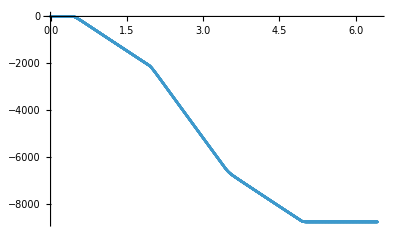

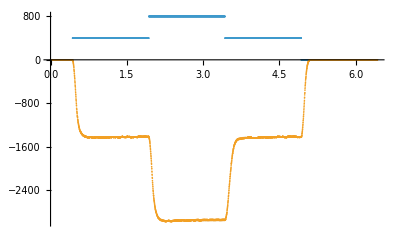

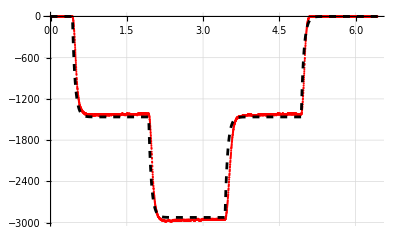

```mathematica
data=Import["/Users/francesco/Documents/Arduino/bilancino/speed_control/csv/left_motor.csv"];
time=data[[2;;,1]]*10^-6;
ticks=data[[2;;,2]];
ref=data[[2;;,3]];
speed=Table[(ticks[[i+1]]-ticks[[i]])/(time[[i+1]]-time[[i]]),{i,1,Length[time]-1}]//N;
w=40;
speedFiltered=MovingAverage[speed,w];
time=time[[w;;-2]];
time=time-time[[1]];
ticks=ticks[[w;;-2]];
ref=ref[[w;;-2]];
p1=ListPlot[{time,ticks}//Transpose]
p2=ListPlot[{{time,ref}//Transpose,{time,speedFiltered}//Transpose}]
p3=ListPlot[{time,speedFiltered}//Transpose,PlotStyle->{Red}];
motor=TransferFunctionModel[k/(s+a),s]/.{k->-71.3,a->19.5}
out=OutputResponse[motor,Interpolation[Transpose[{time,ref}],InterpolationOrder->0][t],{t,time[[1]],time[[-1]]}];
p4=Plot[out,{t,time[[1]],time[[-1]]},PlotStyle->{Dashed,Black}];
Show[{p3,p4},GridLines->Automatic]
```

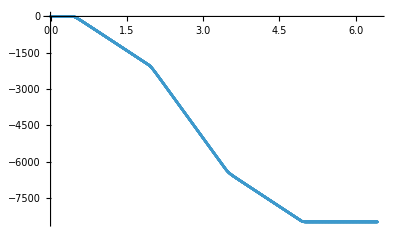

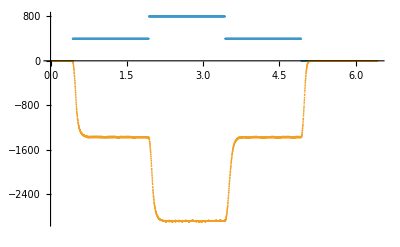

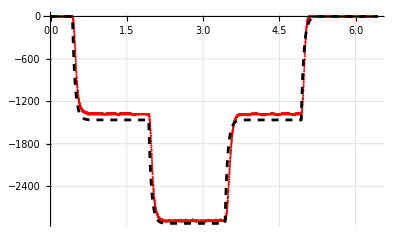

```mathematica
data=Import["/Users/francesco/Documents/Arduino/bilancino/speed_control/csv/right_motor.csv"];
time=data[[2;;,1]]*10^-6;
ticks=data[[2;;,2]];
ref=data[[2;;,3]];
speed=Table[(ticks[[i+1]]-ticks[[i]])/(time[[i+1]]-time[[i]]),{i,1,Length[time]-1}]//N;
w=40;
speedFiltered=MovingAverage[speed,w];
time=time[[w;;-2]];
time=time-time[[1]];
ticks=ticks[[w;;-2]];
ref=ref[[w;;-2]];
p1=ListPlot[{time,ticks}//Transpose]
p2=ListPlot[{{time,ref}//Transpose,{time,speedFiltered}//Transpose}]
p3=ListPlot[{time,speedFiltered}//Transpose,PlotStyle->{Red}];
motor=TransferFunctionModel[k/(s+a),s]/.{k->-71.3,a->19.5}
out=OutputResponse[motor,Interpolation[Transpose[{time,ref}],InterpolationOrder->0][t],{t,time[[1]],time[[-1]]}];
p4=Plot[out,{t,time[[1]],time[[-1]]},PlotStyle->{Dashed,Black}];
Show[{p3,p4},GridLines->Automatic]
```

```mathematica
(*Controllo*)
plant=motor
```

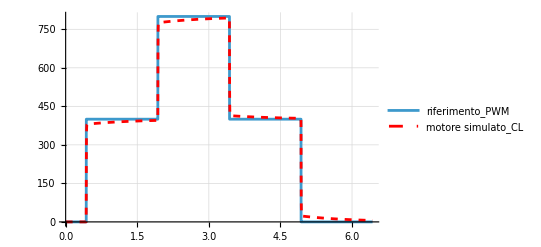

```mathematica
control=TransferFunctionModel[ki/s+kp,s];
openLoop=SystemsModelSeriesConnect[control,plant];
clPlant=SystemsModelFeedbackConnect[openLoop]/.{ki->-5,kp->-5}
out=OutputResponse[clPlant,Interpolation[Transpose[{time,ref}],InterpolationOrder->0][t],{t,time[[1]],time[[-1]]}];
p5=Plot[out,{t,time[[1]],time[[-1]]},PlotStyle->{Dashed,Red},PlotLegends->{"motore simulato_CL"}];
pref=ListLinePlot[{time,ref}//Transpose,PlotLegends->{"riferimento_PWM"}];
Show[{pref,p5},GridLines->Automatic]
```

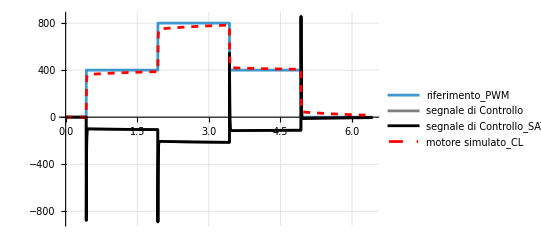

```mathematica
cp=NonlinearStateSpaceModel[{{},{u1-u2}},{},{u1,u2}];
(*sat=NonlinearStateSpaceModel[{
{},Clip[u,{-1023,1023}]
},{},u];*)
sat=NonlinearStateSpaceModel[{
0,u
},x,u];
ccontrol=control/.{ki->-2,kp->-2.5};
clPlant2=SystemsConnectionsModel[{cp,ccontrol,sat,plant},
{(*connessioni*)
{1,1}->{2,1}(*cp->control*),
{2,1}->{3,1}(*control->sat*),
{3,1}->{4,1}(*sat->plant*),
{4,1}->{1,2}(*plant->cp RETROAZIONE*)
},
{(*ingressi*)
{1,1}(*riferimento->cp*)
},
{(*uscite*)
{2,1}(*segnale di controllo*),
{3,1}(*segnale controllo saturato*),
{4,1}(*uscita motore*)
}
];
clPlant2=SystemsModelMerge[clPlant2];
out=OutputResponse[clPlant2,Interpolation[Transpose[{time,ref}],InterpolationOrder->0][t],{t,time[[1]],time[[-1]]}];

p6=Plot[out,{t,time[[1]],time[[-1]]},PlotStyle->{{Gray},{Black},{Dashed,Red}},PlotLegends->{"segnale di Controllo","segnale di Controllo_SAT","motore simulato_CL"},PlotRange->All,GridLines->Automatic];
Show[{pref,p6},GridLines->Automatic,PlotRange->All]
```